```mathematica
encodeID[expr_]:=StringReplace[Developer`EncodeBase64@BinarySerialize@expr,"/"->"~"]
decodeID[expr_]:=BinaryDeserialize@Developer`DecodeBase64ToByteArray@StringReplace[expr,"~"->"/"]
```

```mathematica
ClearAll[getFileNames,fromFileNameGetGeoRange]

getFileNames[folderName_] := 
	FileNames["*.png",FileNameJoin[{NotebookDirectory[],folderName}],Infinity];

fromFileNameGetGeoRange[fileName_] := 
	decodeID[FileBaseName@fileName]["GeoRange"];
```

```mathematica
ClearAll[associateFilesToGeoRange]
associateFilesToGeoRange[fileNames_] := 
	Map[
		File[#] -> fromFileNameGetGeoRange[#] &,
		getFileNames[fileNames]
	]
```

```mathematica
ClearAll[sortPerformance]
sortPerformance[net_,data_] := 
	With[
		{img = Map[Import,data[[All,1]]], correspondingScale = data[[All,2]]},
		SortBy[
			AssociationThread[img,Transpose[{net[img],correspondingScale}]],
			Abs[First[#] - Last[#]]&
		]
	]
```

```mathematica
calculateError[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])/data[[All,2]]//Mean
calculateMeanSq[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])^2//Mean
```

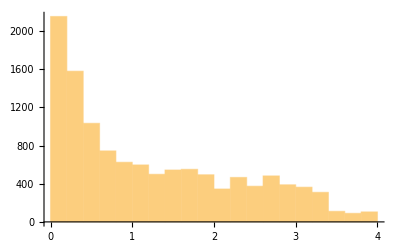
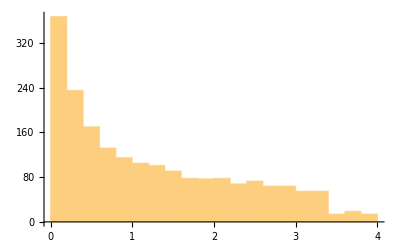
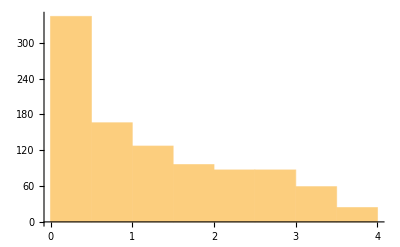
Training Data distribution | Validation Data distribution | Testing Data distribution
-Graphics- | -Graphics- | -Graphics-

```mathematica
ClearAll[training,validation,testing]
ClearAll[trainSmall,validationSmall,testSmall]


training = associateFilesToGeoRange["training"];
validation = associateFilesToGeoRange["validation"];
testing = associateFilesToGeoRange["testing"];

trainSmall = RandomSample@Normal@Select[Association@training,#<=4&];
validationSmall = RandomSample@Normal@Select[Association@validation,#<=4&];
testSmall = RandomSample@Normal@Select[Association@testing,#<=4&];

(*Grid[
	{{"Length","Training","Validation","Testing"},
	{Length@training,Length@validation,Length@testing},
	{Length@trainSmall,Length@validationSmall,Length@testSmall}}
]

TableForm[
	{{"Training Data distribution","Validation Data distribution","Testing Data distribution"},
	{Histogram[Sort@trainSmall[[All,2]]],Histogram[Sort@validationSmall[[All,2]]],Histogram[Sort@testSmall[[All,2]]]}}
]*)


TableForm[
	{{"Training Data distribution","Validation Data distribution","Testing Data distribution"},
	{Histogram[trainSmall[[All,2]]],Histogram[validationSmall[[All,2]]],Histogram[testSmall[[All,2]]]}}
]
```

```mathematica
tr = Join[trainSmall,training1,training2];
vl = Join[validationSmall,validation1,validation2];
te = Join[testSmall,testing1,testing2];

tr // Length
vl // Length
te // Length
```

33162

4075

1830

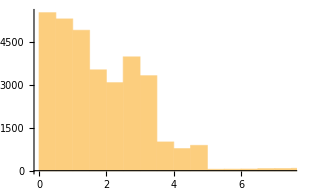
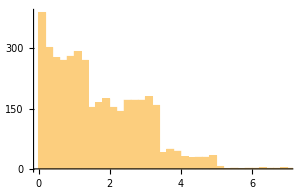
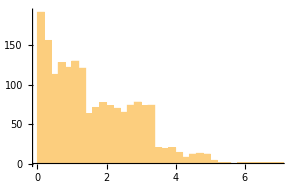
Training Data distribution | Validation Data distribution | Testing Data distribution
-Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[
	{{"Training Data distribution","Validation Data distribution","Testing Data distribution"},
	{Histogram[tr[[All,2]]],Histogram[vl[[All,2]]],Histogram[te[[All,2]]]}}
]
```

```mathematica
ClearAll[tnet]
tnet = Import[FileNameJoin[{NotebookDirectory[],"amazonTrainedNet.wlnet"}]]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
ClearAll[dataset1]
dataset1 = sortPerformance[tnet,testSmall];
```

```mathematica
dataset1[[1;;4]]  (*Best 3*)
dataset1[[-14;;-11]] (*Worst 3*)
```

<|-Graphics-→{2.7444,2.74455},-Graphics-→{0.468401,0.469929},-Graphics-→{1.07208,1.07445},-Graphics-→{0.414134,0.416545}|>

<|-Graphics-→{1.71616,2.61353},-Graphics-→{3.04402,3.99781},-Graphics-→{2.85387,3.88059},-Graphics-→{0.5854,1.74235}|>

```mathematica
Repeated
```

```mathematica
TableForm[
	{Normal@dataset1[[1;;2]],
	Normal@dataset1[[-12;;-11]]},TableHeadings->{{"Best","Worst"},{"Image        -         Scale  -  Predicted","Image        -         Scale  -  Predicted"}}
]
```

| Image        -         Scale  -  Predicted | Image        -         Scale  -  Predicted
Best | -Graphics-→{2.7444,2.74455} | -Graphics-→{0.468401,0.469929}
Worst | -Graphics-→{2.85387,3.88059} | -Graphics-→{0.5854,1.74235}

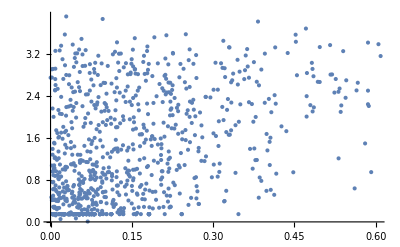

```mathematica
ListPlot[Transpose[{Map[Abs[First[#]-Last[#]]&,Values[dataset1]],Map[First[#]&,Values[dataset1]]}]]
```

```mathematica
calculateError[tnet,testSmall]
```

0.299825